# Anisotropy-Assisted Quasi-Phase Matching (AA-QPM)

## Coupled Mode Theory for Second Harmonic Generation

### With Pump Depletion

#### Defining the main parameters

```mathematica
n =2;
deff=3.5*10^-3;(*m/V*)
c=299792458;(*m/s*)
omega = c/(1.55*10^-6);(*rad/s*)
k1 = 2Pi*n/((1.55*10^-6));(*rad/m*)
k2 =0.99*2Pi*n/((0.5*1.55*10^-6))(*rad/m*);
```

#### Writing the system of coupled equations

First we write a solution with a slight mismatch:

```mathematica
sol1=NDSolve[
{
A1'[z]==((2*I*omega^2*deff)/(k1*c^2))*A2[z]Conjugate[A1[z]]*Exp[I*(k2-2*k1)*z],
A2'[z]==((I*(2*omega)^2*deff)/(k2*c^2))*(A1[z])^2 Exp[-I*(k2-2*k1)*z],
A1[0]==1,
A2[0]==0
},
{A1,A2},
{z,0,10^-3}];
```

Now we write a second solution with a perfect phase-matching (just eliminate the complex exponential term).

```mathematica
sol2=NDSolve[
{
A1'[z]==((2*I*omega^2*deff)/(k1*c^2))*A2[z]Conjugate[A1[z]],
A2'[z]==((I*(2*omega)^2*deff)/(k2*c^2))*(A1[z])^2,
A1[0]==1,
A2[0]==0
},
{A1,A2},
{z,0,10^-3}];
```

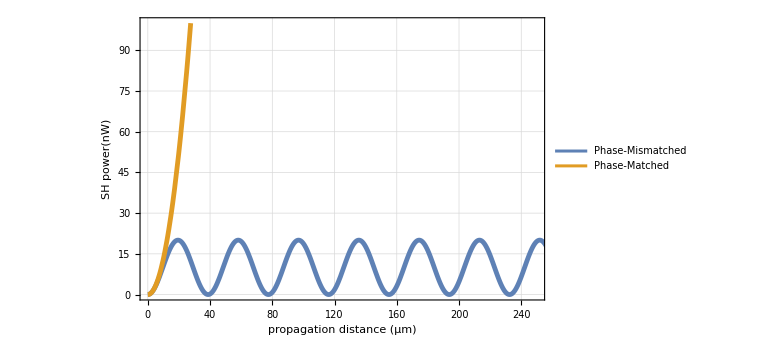

```mathematica
Plot[{10^6*Evaluate[{Abs[A2[z*10^-6]]^2}/. sol1],10^6*Evaluate[{Abs[A2[z*10^-6]]^2}/. sol2]},{z,0,1000},PlotTheme->"Detailed",LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->Thickness[0.006],FrameLabel->{"propagation distance (μm)","SH power(nW)"},PlotRange->{{0,250},{0,100}},ImageSize->Large,PlotLegends->Placed[{"Phase-Mismatched","Phase-Matched"}, Above]]
```

## Modelling QPM and calculating it’s efficiency

### Susceptibility Modulation

In traditional QPM, we simply invert the sign of the nonlinear susceptibility with the appropriate periodicity. Numerically, we will represent this by a square wave through its Fourier Series expansion.

Clearly, to compensate the phase mismatch, the period must be:

```mathematica
(2*Pi)/(k2-2*k1)*10^6
```

-38.75

Now we can plot the factor that will multiply the susceptibility

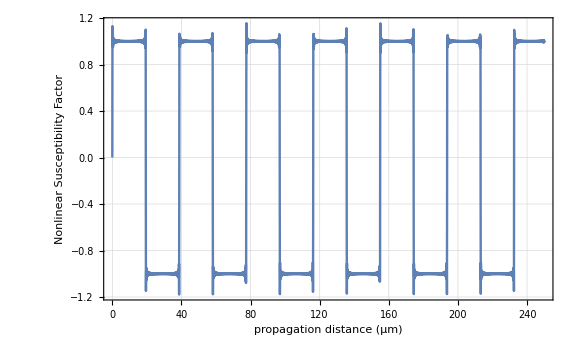

```mathematica
Plot[4/Pi Sum[1/(2*n-1)Sin[((2*n-1)*Pi*z*10^-6)/Abs[Pi/(k2-2*k1)]],{n,1,100}],{z,0,250},PlotTheme->"Detailed",ImageSize->Large,LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->Thickness[0.003],FrameLabel->{"propagation distance (μm)","Nonlinear Susceptibility Factor"},PlotLegends->None,PlotRange->{{0,250},Automatic},ImageSize->Large]
```

And we can add this to the solution

### Simulating QPM

```mathematica
sol3=NDSolve[
{
A1'[z]==((2*I*omega^2*deff*4/Pi Sum[1/(2*n-1)Sin[((2*n-1)*Pi*z)/Abs[Pi/(k2-2*k1)]],{n,1,10}])/(k1*c^2))*A2[z]Conjugate[A1[z]]*Exp[I*(k2-2*k1)*z],
A2'[z]==((I*(2*omega)^2*deff*4/Pi Sum[1/(2*n-1)Sin[((2*n-1)*Pi*z)/Abs[Pi/(k2-2*k1)]],{n,1,10}])/(k2*c^2))*(A1[z])^2 Exp[-I*(k2-2*k1)*z],
A1[0]==1,
A2[0]==0
},
{A1,A2},
{z,0,10^-3}];
```

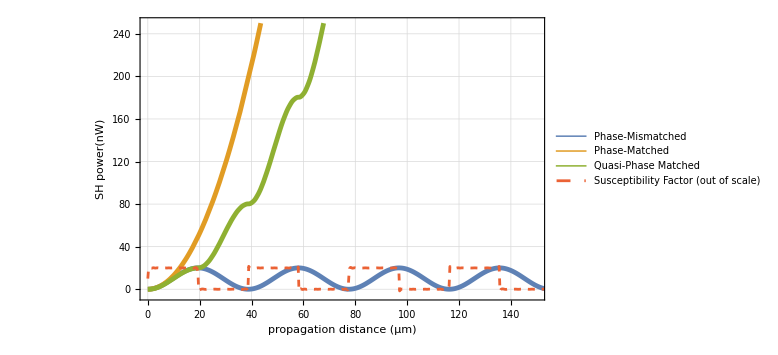

```mathematica
Plot[
{10^6*Evaluate[{Abs[A2[z*10^-6]]^2}/. sol1],
10^6*Evaluate[{Abs[A2[z*10^-6]]^2}/. sol2],
10^6*Evaluate[{Abs[A2[z*10^-6]]^2}/. sol3],
10+10*4/Pi Sum[1/(2*n-1)Sin[((2*n-1)*Pi*z*10^-6)/Abs[Pi/(k2-2*k1)]],{n,1,50}]
},{z,0,1000},PlotTheme->"Detailed",LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->{Thickness[0.006],Thickness[0.006],Thickness[0.006],{Dashed}},FrameLabel->{"propagation distance (μm)","SH power(nW)"},PlotRange->{{0,150},{-5,250}},ImageSize->Large,PlotLegends->Placed[{"Phase-Mismatched","Phase-Matched","Quasi-Phase Matched","Susceptibility Factor (out of scale)"}, Right]]
```

### Calculating the efficiency

In this section, we compare the efficiency of each method by plotting their ratio with respect to the perfectly phase-matched case. As expected, they all approach a finite value after a certain distance, we can calculate this ratio at sufficiently large z to get an estimate for the efficiency (this number can be calculated explicitly by writing out the effective nonlienarity as a Fourier series). It is instructive to compare the plot below to the one imediately above this section, and see how the absolute values evolve with propagation.

Obs.: the ratios above are plotted starting at z = 8 μm, to avoid numerical artifacts introduced near z=0.

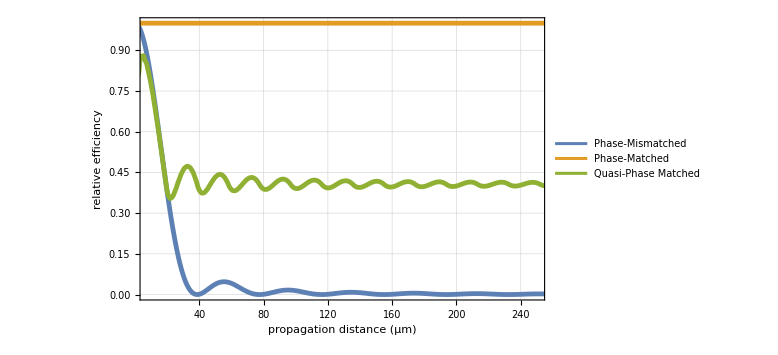

```mathematica
Plot[
{Evaluate[{Abs[A2[z*10^-6]]^2}/. sol1]/Evaluate[{Abs[A2[z*10^-6]]^2}/. sol2],
Evaluate[{Abs[A2[z*10^-6]]^2}/. sol2]/Evaluate[{Abs[A2[z*10^-6]]^2}/. sol2],
Evaluate[{Abs[A2[z*10^-6]]^2}/. sol3]/Evaluate[{Abs[A2[z*10^-6]]^2}/. sol2],
},{z,0,1000},PlotTheme->"Detailed",LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->{Thickness[0.006],Thickness[0.006],Thickness[0.006],{Dashed}},FrameLabel->{"propagation distance (μm)","relative efficiency"},PlotRange->{{8,250},{Automatic,Automatic}},ImageSize->Large,PlotLegends->Placed[{"Phase-Mismatched","Phase-Matched","Quasi-Phase Matched"}, Right]]
```

## Extracting Effective Nonlinearity from a Path Shape

### Susceptibility Tensor and the Overlap Integral

The second order nonlinear susceptibility tensor, in contracted notation, is given by (see starthere.pdf file for derivation):

```mathematica
d=({{0, 0, 0, 0, d31, -d22}, {-d22, d22, 0, d31, 0, 0}, {d31, d31, d33, 0, 0, 0}});
```

```mathematica
MatrixForm[d]
```

(0 | 0 | 0 | 0 | d31 | -d22
-d22 | d22 | 0 | d31 | 0 | 0
d31 | d31 | d33 | 0 | 0 | 0)

In the spatial overlap integral that appears in the coupled mode formalism (see pdf file), we see a term that involves a product between the components of the nonlinear polarization, the susceptibility tensor and the pump field components squared. Let us write out each factor in this product.

```mathematica
EpumpSq=({{E1^2}, {E2^2}, {E3^2}, {2*E2*E3}, {2*E3*E1}, {2*E1*E2}});
```

```mathematica
MatrixForm[EpumpSq]
```

(E1^2
E2^2
E3^2
2 E2 E3
2 E1 E3
2 E1 E2)

And the generated second harmonic field components (nonlinear polarization)

```mathematica
Esecondharmonic=({{P1}, {P2}, {P3}});
```

```mathematica
MatrixForm[Esecondharmonic]
```

(P1
P2
P3)

The final expression in the overlap integral is

```mathematica
Dot[Transpose[Esecondharmonic],dE]
```

{{(-2 d22 E1 E2+2 d31 E1 E3) P1+(-d22 E1^2+d22 E2^2+2 d31 E2 E3) P2+(d31 E1^2+d31 E2^2+d33 E3^2) P3}}

### Rotating the frame of reference

For the case of Thin-Film Lithium Niobate, anisotropy assisted quasi-matching requires both the susceptibility anistropy and the electric field to be contained in-plane. Thus, it is only feasible for x-cut lithium niobate, and for interactions between quasi-TE modes (such that the optical mode is polarized in the xy plane).

Consider, for example, a path described by a trigonometric function, as in

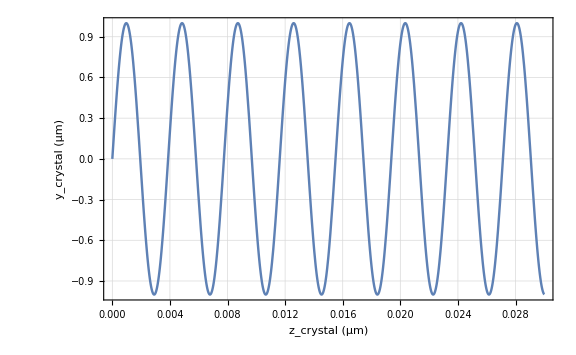

```mathematica
k1 = 2Pi*n/((1.55*10^-6));
k2 =0.9999*2Pi*n/((0.5*1.55*10^-6));
Plot[Sin[z/Abs[1/(k2-2*k1)]],{z,0,0.03},PlotTheme->"Detailed",ImageSize->Large,LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->Thickness[0.003],FrameLabel->{"z_crystal (μm)","y_crystal (μm)","top-view of AA-QPM waveguide"},PlotLegends->None,PlotRange->{{0,0.03},Automatic}]
```

Notice that the coordinates above are relative to the crystal orientation. For the optical mode, we can adopt a frame of reference that goes along with the field, such that the wavevector always points in the z-direction.

In this frame, the amount of optical power in each polarization components is constant, but the effective nonlinear susceptibility will change, as the component of electric field in the direction of each crystalline axis will be modulated by path shape.

If we define θ as the angle between the propagation direction and the z-axis (the optical axis for lithium niobate), then we can see that (for a TE mode), the field amount in each crystalline direction is given by

E_(z,crystal)=E_(y, mode frame)sin(θ)
E_(y,crystal)=E_(y mode frame)cos(θ)

Here, we are assuming a field that is initially polarized only in the y-direction, and the power is then distributed among he polarization components as the path is varied. The crystalline x-direction and and the x-direction in the moving “mode frame” remain aligned. When dealing with the TE mode, we can approximate that all field components in this direction are zero.

If the field were not perfectly polarized in the y-direction (as is the case in a quasi-TE mode), when can simply add an offset constant value to θ to account for this. This value could be obtained in a standard FEM simulation by calculating the ratio of the y and z polarization components at each point in the waveguide mode profile.

In the matrices derived above, we were dealing only with the crystal frame of reference. Now, the terms in the overlap integral become

```mathematica
d=({{0, 0, 0, 0, d31, -d22}, {-d22, d22, 0, d31, 0, 0}, {d31, d31, d33, 0, 0, 0}});
EpumpSqRot[θ_]:=({{0}, {Ey^2*Cos[θ]^2}, {Ey^2*Sin[θ]^2}, {2*Ey*Ey*Cos[θ]*Sin[θ]}, {0}, {0}});
EsecondharmonicRot[θ_]:=({{0}, {Ey*Cos[θ]}, {Ey*Sin[θ]}});
```

Now, once we compute the multiplications, we obtain:

```mathematica
Simplify[Dot[Transpose[EsecondharmonicRot[θ]],d.EpumpSqRot[θ]][[1,1]]]
```

Ey^3 (d22 Cos[θ]^3+3 d31 Cos[θ]^2 Sin[θ]+d33 Sin[θ]^3)

Therefore, all of the frame rotation can be accounted for in the model simply by defining an effective nonlinear susceptibility as a function of θ:

```mathematica
deffrot[d22_,d31_,d33_,θ_]:=(d22 Cos[θ]^3+3 d31 Cos[θ]^2 Sin[θ]+d33 Sin[θ]^3);
```

### Parametrizing the path

Return once again to the sinusoidal path suggested in the previous section

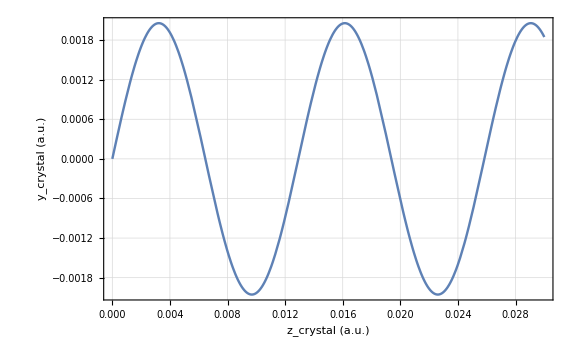

```mathematica
Plot[Abs[1/(k2-2*k1)]Sin[z/Abs[1/(k2-2*k1)]],{z,0,0.03},PlotTheme->"Detailed",ImageSize->Large,LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->Thickness[0.003],FrameLabel->{"z_crystal (a.u.)","y_crystal (a.u.)","top-view of AA-QPM waveguide"},PlotLegends->None,PlotRange->{{0,0.03},Automatic}]
```

We can calculate the angle θ at each point by taking the derivative of the path function:

```mathematica
p[z_]:=Abs[1/(k2-2*k1)]Sin[z/Abs[1/(k2-2*k1)]];
```

Clearly, the propagation direction is the direction tangent to the curve. The angle with respect to the z-axis is therefore

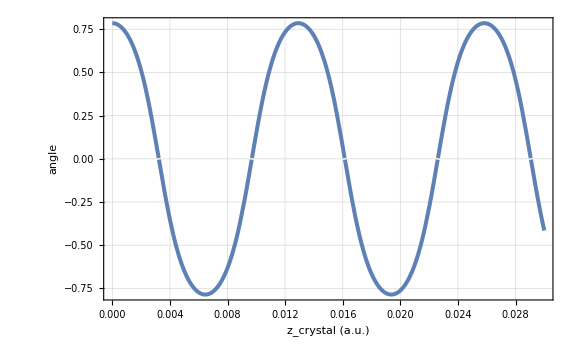

```mathematica
With[
{
θ=ArcTan[D[p[z],z]]
}
,
Plot[{θ},{z,0,0.03},PlotTheme->"Detailed",ImageSize->Large,LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->Thickness[0.005],FrameLabel->{"z_crystal (a.u.)","angle"},PlotLegends->None,PlotRange->{All,All}]]
```

And with this information, we can directly calculate the effective nonlinear susceptibility. Using d22 = 3.07pm/V, d31 = 5.95 pm/V, d33 = 34.4 pm/V

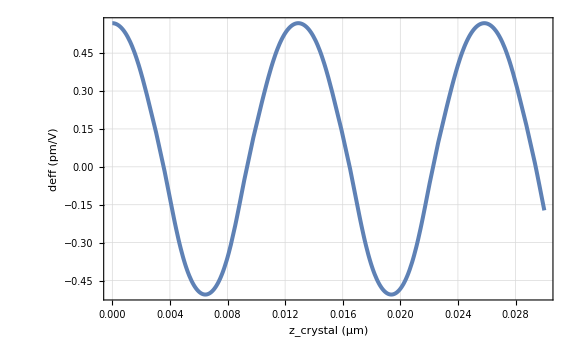

```mathematica
With[
{
θ=ArcTan[D[p[z],z]]
}
,
Plot[1/34.4{34.4*Sin[θ]^3+3.07*Cos[θ]^3+3*5.95*Cos[θ]^2*Sin[θ]},{z,0,0.03},PlotTheme->"Detailed",ImageSize->Large,LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->Thickness[0.005],FrameLabel->{"z_crystal (μm)","deff (pm/V)"},PlotLegends->None,PlotRange->{{0,0.03},Automatic}]]
```

### Simulating AA-QPM

Now we simply plug this in directly into the model to estimate the efficiency of AA-QPM with a sinusoidal path.

#### Sol1: Quasi-phase matched

```mathematica
n =2;
c=299792458;
deff=0.5*10^-3;
omega = c/(1.55*10^-6);
k1 = 2Pi*n/((1.55*10^-6));
k2 =0.99997*2Pi*n/((0.5*1.55*10^-6));
sol1=NDSolve[{A2'[z]==((I*(2*omega)^2*deff*4/Pi Sum[1/(2*n-1)Sin[((2*n-1)*Pi*z)/Abs[Pi/(k2-2*k1)]],{n,1,8}])/(k2*c^2))*Exp[I*(k2-2*k1)*z],A2[0]==0},
{A2},{z,0,1}];
```

#### Sol2: Phase-matched

```mathematica
n =2;
c=299792458;
deff=0.5*10^-3;
omega = c/(1.55*10^-6);
k1 = 2Pi*n/((1.55*10^-6));
k2 =2Pi*n/((0.5*1.55*10^-6));
sol2=NDSolve[{A2'[z]==((I*(2*omega)^2*deff)/(k2*c^2))*Exp[I*(k2-2*k1)*z],A2[0]==0},
{A2},{z,0,1}];
```

#### Sol3: Phase-mismatched

```mathematica
n =2;
c=299792458;
deff=0.5*10^-3;
omega = c/(1.55*10^-6);
k1 = 2Pi*n/((1.55*10^-6));
k2 =0.99997*2Pi*n/((0.5*1.55*10^-6));
sol3=NDSolve[{A2'[z]==((I*(2*omega)^2*deff)/(k2*c^2))*Exp[I*(k2-2*k1)*z],A2[0]==0},
{A2},{z,0,1}];
```

#### Sol4: AA-QPM

```mathematica
θ[z_]:=ArcTan[Cos[z/Abs[1/(k2-2*k1)]]];
n =2;
c=299792458;
deff=0.5*10^-3;
omega = c/(1.55*10^-6);
k1 = 2Pi*n/((1.55*10^-6));
k2 =0.99997*2Pi*n/((0.5*1.55*10^-6));
sol4=NDSolve[{A2'[z]==((I*(2*omega)^2*deff*1/34.4(34.4*Sin[θ[z]]^3+3.07*Cos[θ[z]]^3+3*5.95*Cos[θ[z]]^2*Sin[θ[z]]))/(k2*c^2))*Exp[I*(k2-2*k1)*z],A2[0]==0},
{A2},{z,0,1}];
```

#### Plots

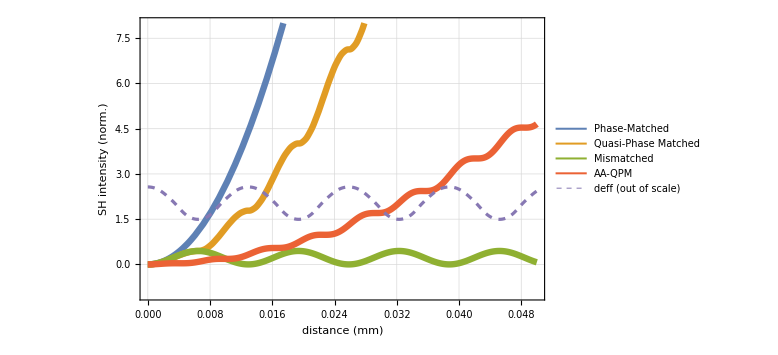

```mathematica
pl1=Plot[{
10*Evaluate[{Abs[A2[z]]^2}/. sol2],
10*Evaluate[{Abs[A2[z]]^2}/. sol1],
10*Evaluate[{Abs[A2[z]]^2}/. sol3],
10*Evaluate[{Abs[A2[z]]^2}/. sol4],
2+1/34.4(34.4*Sin[θ[z]]^3+3.07*Cos[θ[z]]^3+3*5.95*Cos[θ[z]]^2*Sin[θ[z]])
},
{z,0,0.05},PlotTheme->"Detailed",PlotLegends->{"Phase-Matched","Quasi-Phase Matched","Mismatched","AA-QPM","deff (out of scale)"},LabelStyle->{FontFamily->"Calibri",16,Black},PlotRange->{{0.00,0.05},{-1,8}},ImageSize->Large,PlotStyle->{Thickness[0.008],Thickness[0.008],Thickness[0.008],Thickness[0.008],{Thickness[0.004],Dashed},{Thickness[0.004],Dashed}},FrameLabel->{"distance (mm)","SH intensity (norm.)"}]
```

#### Calculating the efficiency of AA-QPM

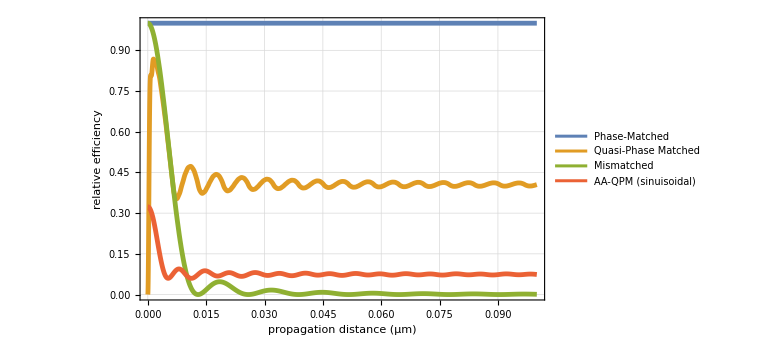

```mathematica
Plot[
{Evaluate[{Abs[A2[z]]^2}/. sol2]/Evaluate[{Abs[A2[z]]^2}/. sol2],
Evaluate[{Abs[A2[z]]^2}/. sol1]/Evaluate[{Abs[A2[z]]^2}/. sol2],
Evaluate[{Abs[A2[z]]^2}/. sol3]/Evaluate[{Abs[A2[z]]^2}/. sol2],
Evaluate[{Abs[A2[z]]^2}/. sol4]/Evaluate[{Abs[A2[z]]^2}/. sol2]
},{z,0,0.1},PlotTheme->"Detailed",LabelStyle->{FontFamily->"Calibri",20,Black},PlotStyle->{Thickness[0.006],Thickness[0.006],Thickness[0.006],Thickness[0.006]},FrameLabel->{"propagation distance (μm)","relative efficiency"},PlotRange->{{Automatic,0.1},{Automatic,Automatic}},ImageSize->Large,PlotLegends->Placed[{"Phase-Matched","Quasi-Phase Matched","Mismatched","AA-QPM (sinuisoidal)"}, Right]]
```

## Final Remarks

A model was introduced and implemented to quantify the efficiency of anisotropy-assisted quasi-phase matching (AA-QPM). The results indicate that nonlinear conversion can in fact be achieved between initially mismatched modes simply by modulating the optical path in the two-dimensional plane. Obtaining the optimal path to achieve this is an open question, as a trade-off must be considered between maximum theoretical efficiency according to this model, and the actual efficiency in a device where the curvature radius, dispersion characteristics and cross-talk effects will be relevant. Nevertheless, this model itself can be used for an iterated “inverse design”-like process of searching for the ideal path shape.

Overall, the central advantage of AA-QPM is that it can reduce fabrication complexity significantly. In comparison of electric-field induced poling, for example, If the reduced efficiency is acceptable, this technique can eliminate an additional step of aligned lithography, the deposition, lift-off and removal of metal contacts (which often contaminate the sample and lead to increased optical loss) and the cumbersome process of applying electric pulses with the correct waveform and at the correct temperature.